## Numerical results for trophical transmission model with multiple infections (must run)

```mathematica
SetDirectory[NotebookDirectory[]]
<<Tools`
ParallelNeeds["Tools`"](* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/multipleinfections/code

# ODEs (must run)

```mathematica
dIsdt = R[Iw, Is, Iww]- d Is- Πs[Ds, Dw, Dww] Is  - ηw  Is ;
dIwdt =  (1-p)ηw Is  - (d + αw)Iw - Πw[Ds, Dw,Dww, βw]Iw; 
dIwwdt =  p ηw Is  - (d + αww)Iww - Πww[Ds, Dw, Dww,βww]Iww; 
dDsdt =B[Ds, Dw,Dww, Is, Iw, Iww]  - μ Ds - (λww + λw) Ds;
dDwdt =(λw + 2(1-q)λww) Ds- (μ + σw) Dw - (2(1-q)λww +λw)Dw;
dDwwdt = q λww Ds + (2(1-q)λww + λw)Dw - (μ + σww)Dww;
dWdt = fw Dw +fww Dww- δ W - ηw Is;

forceInf = {ηw -> γ W, λw -> βw Iw, λww -> βww Iww};
odesRes = {dIsdt, dIwdt, dIwwdt, dDsdt, dDwdt, dDwwdt, dWdt};
varRes = {Is, Iw, Iww, Ds, Dw, Dww, W};
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
```

# Reproduction ratio R0

```mathematica
R0ww = Is γ (p  q βww)/(d+αww+Πww[Ds, Dw, Dww,βww]) Ds/(μ+σww)fww/(Is γ+δ);
R0w = Is γ (((1-p) βw)/(d+αw+ Πw[Ds, Dw,Dww, βw])+(2 p (1-q)  βww)/(d+αww+Πww[Ds, Dw, Dww,βww]))Ds/( βw Iw-2 (-1+q)  βww Iww+μ+σw)fw/(Is γ+δ);
R0 = R0ww  + R0w;
```

# Graph format and parallel computation (must run)

```mathematica
includeFrame = True(*{{True, False}, {True,False}}*);
imageSize = 600;
frameStyle = Directive[Black,Thickness[0.003]];
labelStyle = {Black, FontSize-> 14};
colorlist = ColorData[97,"ColorList"]
colorstable = ColorData[97,"ColorList"][[{1, 2, -2}]]
ihostCol = ColorData[97,"ColorList"][[1]];
 dhostCol = ColorData[97,"ColorList"][[4]];
fCol1 = ColorData[97,"ColorList"][[3]];
fCol2 = ColorData[97,"ColorList"][[-1]];
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.736782672705901, 0.358, 0.5030266573755369]}

# Linear birth function for intermediate host

```mathematica
func0 = {R[Iw, Is, Iww] -> r(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  βw(Ds + Dw+Dww),Πww[Ds, Dw,Dww, βww]->  βww(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
sysfunc0 = odesRes/.forceInf/.func0;
sysNDSolvefunc0 = MakeSystem[varRes, t,sysfunc0];
```

## Jacobian matrix

```mathematica
Jmatfunc0 = D[sysfunc0, {varRes}];
```

## Ecological trajectories

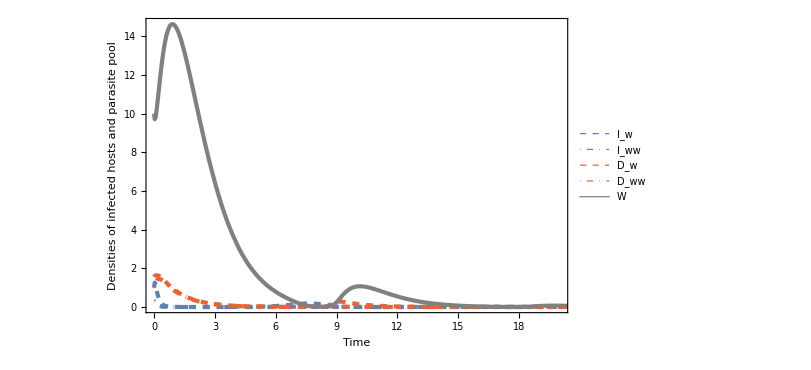
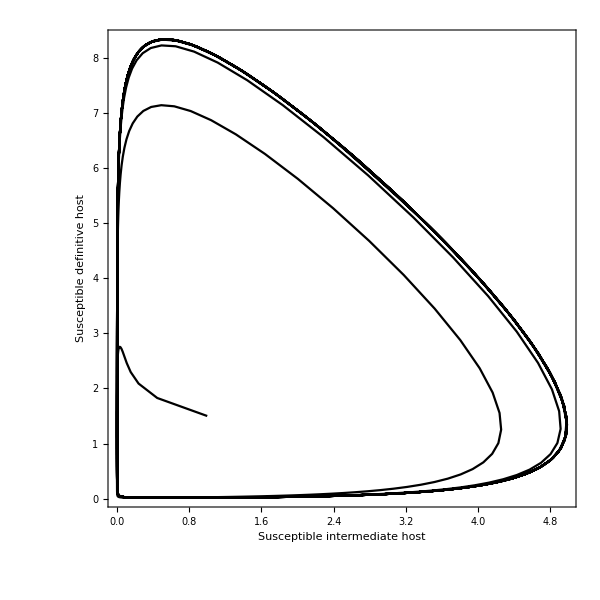
-Graphics- | -Graphics-

```mathematica
prEco0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 0.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 6.5,fww-> 7.5, δ-> 0.9};

maxt = 100;

init0= {Is[0]== 1, Iw[0] == 1,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 10};

sols0 = NSolve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes];
ndsol0 = NDSolve[Join[sysNDSolvefunc0/.prEco0, init0], varRes, {t, 0, maxt}] ;

range = {{-1, 20},{-1, 20}};
trajectStyle = {{ihostCol, Dashed,Thickness[0.005]}, {ihostCol, DotDashed,Thickness[0.005]}, {dhostCol, Dashed,Thickness[0.005]}, {dhostCol, DotDashed,Thickness[0.005]}, {Gray, Thickness[0.005]}};
p1 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, 20}, All},PlotLegends->{"I_w", "I_ww", "D_w", "D_ww", "W"}, FrameLabel->{Style["Time",Black,24],Style["Densities of infected hosts\n and parasite pool",Black,24]}, ImageSize->imageSize, Frame-> True,FrameStyle->frameStyle,LabelStyle->labelStyle,PlotStyle->trajectStyle];

p2 = ParametricPlot[{Evaluate[{Is[t], Ds[t]}/.ndsol0]}, {t, 0, maxt}, AspectRatio->1, PlotRange->All, Frame->includeFrame, PlotStyle->Black, FrameStyle->frameStyle, FrameLabel->{Style["Susceptible intermediate host",Black,24], Style["Susceptible definitive host",Black,24]}, ImageSize->imageSize, LabelStyle->labelStyle];

Grid[{{p1, p2}}]
(*Export["diseasefree_linear.jpg",%]*)
```

```mathematica
tabtopl=Table[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsol0]⟦1⟧, {t, 0, maxt,0.01}];
```

```mathematica
ListLinePlot[Transpose[tabtopl],PlotRange->All,MultiaxisArrangement->{{1,2,3,4},5}]
```

ListLinePlot::optx: Unknown option MultiaxisArrangement→{{1,2,3,4},5} in ListLinePlot[«1»].

ListLinePlot[1]
 |  |  |  |

# Nonlinear birth function for intermediate host

```mathematica
func1 = {R[Iw, Is, Iww] -> r(1-k(Is + Iw+Iww))(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  (ρ +βw)(Ds + Dw+ Dww),Πww[Ds, Dw, Dww, βww]->  (ρ+βww)(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};

sysfunc1 = odesRes/.forceInf/.func1;
sysNDSolvefunc1 = MakeSystem[varRes, t, sysfunc1];
```

## Jacobian matrix

```mathematica
Jmatfunc1 = D[sysfunc1, {varRes}];
```

## Ecological trajectories

## Disease free equilibrium

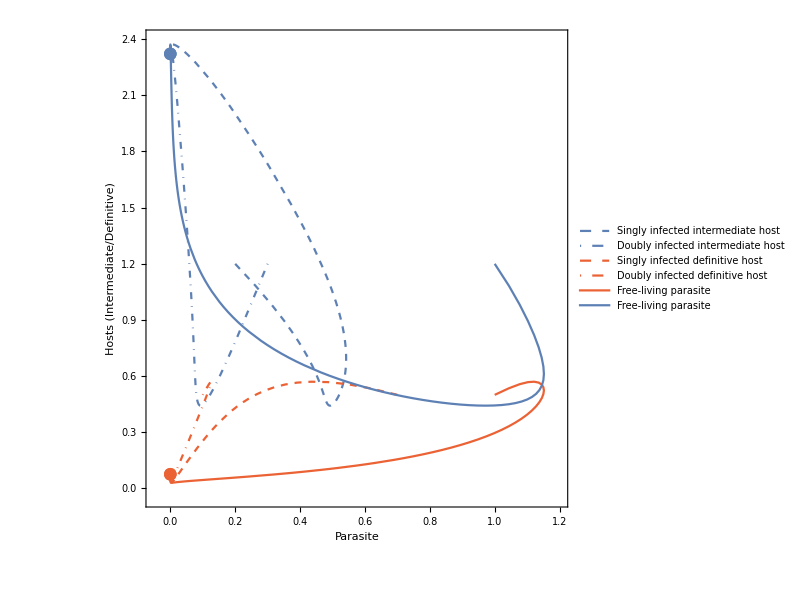

```mathematica
prEcoNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 0.9, k -> 0.26};

maxt = 100;

solsNL = NSolve[Thread[(sysfunc1/.prEcoNL) == 0], varRes];
range = {{-0.05, 1.2}, {-0.05, 2.4}};
{Is[0]== 1.2, Iw[0] == 0.2,Iww[0]==0.3, Ds[0] ==0.5, Dw[0] == 0.7,Dww[0]==0.1, W[0] == 1};
ndsolNL = NDSolve[Join[sysNDSolvefunc1/.prEcoNL, %], varRes, {t, 0, maxt}] ;

trajectStyle = {{ihostCol, Dashed}, {ihostCol, DotDashed}, {dhostCol, Dashed}, {dhostCol, DotDashed}, {dhostCol, Thick}, {ihostCol, Thick}};
pp = ParametricPlot[{Evaluate[{Iw[t], Is[t]}/.ndsolNL], Evaluate[{Iww[t], Is[t]}/.ndsolNL], Evaluate[{Dw[t], Ds[t]}/.ndsolNL], Evaluate[{Dww[t], Ds[t]}/.ndsolNL], Evaluate[{W[t], Ds[t]}/.ndsolNL], Evaluate[{W[t], Is[t]}/.ndsolNL]}, {t, 0, maxt}, AspectRatio->1, Frame->includeFrame, PlotStyle->trajectStyle , FrameStyle -> frameStyle, PlotRange->range, FrameLabel->{"Parasite", "Hosts (Intermediate/Definitive)"}, LabelStyle->labelStyle,   ImageSize->imageSize,PlotLegends-> {"Singly infected intermediate host", "Doubly infected intermediate host", "Singly infected definitive host", "Doubly infected definitive host", "Free-living parasite" ,"Free-living parasite"}];
i1 = Evaluate[Is[maxt]/.ndsolNL][[1]];
i2 = Evaluate[Iw[maxt]/.ndsolNL][[1]];
d1 = Evaluate[Ds[maxt]/.ndsolNL][[1]];
d2 = Evaluate[Dw[maxt]/.ndsolNL][[1]];
point = ListPlot[{{{i2, i1}}, {{d2, d1}}}, PlotStyle->{ihostCol, dhostCol}, PlotMarkers->{"●", Medium}];
g1 = Show[{pp, point}]
```

## Disease stable equilibrium

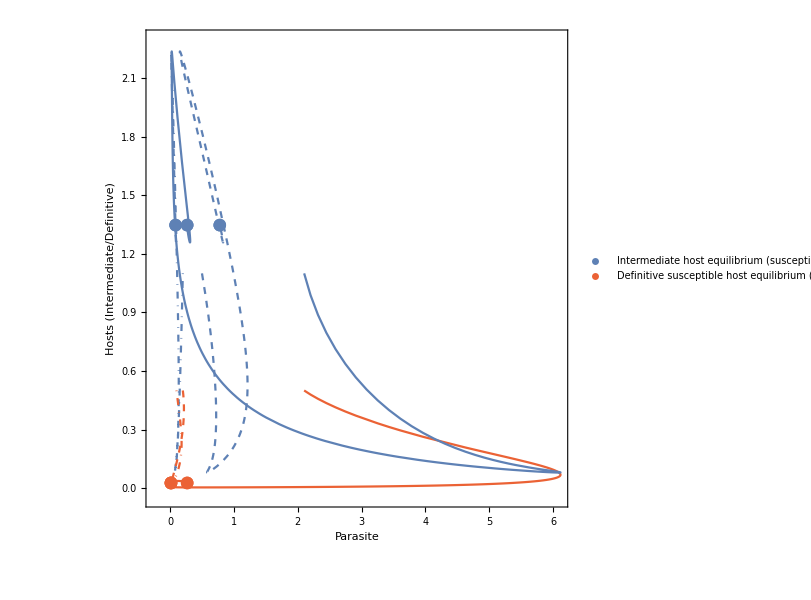

```mathematica
prEcoDSNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, α-> 0, βw-> 4.5, βww-> 4.5,p-> 0.1, c-> 1.4, μ-> 3.9, σ-> 0,q-> 0.01, fw -> 45, fww-> 45,δ-> 0.9, k -> 0.26};



condsimplifyNL = {αw-> α, αww-> α, σw-> σ, σww-> σ};

maxt =60;

range = {{-0.25, 6.1}, {-0.05, 2.3}};
{Is[0]== 1.1, Iw[0] == 0.5,Iww[0]==0.2, Ds[0] ==0.5, Dw[0] == 0.2,Dww[0]==0.1, W[0] == 2.1};
ndsolDS = NDSolve[Join[sysNDSolvefunc1/.condsimplifyNL/.prEcoDSNL, %], varRes, {t, 0, maxt}] ;
trajectStyle = {{ihostCol, Dashed}, {ihostCol, DotDashed}, {dhostCol, Dashed}, {dhostCol, DotDashed}, {dhostCol, Thick}, {ihostCol, Thick}};
Plot[Evaluate[vartRes/.ndsolDS], {t, 0, maxt}, PlotRange->All];
pp1 = ParametricPlot[{Evaluate[{Iw[t], Is[t]}/.ndsolDS], Evaluate[{Iww[t], Is[t]}/.ndsolDS], Evaluate[{Dw[t], Ds[t]}/.ndsolDS], Evaluate[{Dww[t], Ds[t]}/.ndsolDS], Evaluate[{W[t], Ds[t]}/.ndsolDS], Evaluate[{W[t], Is[t]}/.ndsolDS]}, {t, 0, maxt}, AspectRatio->1, Frame->includeFrame, PlotStyle->trajectStyle, FrameStyle -> frameStyle, PlotRange->range, FrameLabel->{"Parasite", "Hosts (Intermediate/Definitive)"}, LabelStyle->labelStyle, ImageSize->imageSize];
w = Evaluate[W[maxt]/.ndsolDS][[1]];
i1 = Evaluate[Iw[maxt]/.ndsolDS][[1]];
i2 = Evaluate[Is[maxt]/.ndsolDS][[1]];
i3 = Evaluate[Iww[maxt]/.ndsolDS][[1]];
d1 = Evaluate[Dw[maxt]/.ndsolDS][[1]];
d2 = Evaluate[Ds[maxt]/.ndsolDS][[1]];
d3 = Evaluate[Dww[maxt]/.ndsolDS][[1]];
point = ListPlot[{{{i1, i2}}, {{d1, d2}}, {{i3, i2}}, {{d3, d2}}, {{w, i2}}, {{w, d2}}}, PlotStyle->{ihostCol, dhostCol, ihostCol, dhostCol}, PlotMarkers->{"●", Medium} , PlotLegends->{"Intermediate host equilibrium \n (susceptible, singly, and doubly infected)", "Definitive susceptible host equilibrium \n (susceptible, singly, and doubly infected)"}];
g2 = Show[{pp1, point}]
```

## Combined disease free and disease stable ecology plot

```mathematica
GraphicsRow[{g1, g2}]
```

-Graphics-

## Bifurcation f_w (f_ww = ϵ f_w)

## Parameter set 1

CALCULATE

```mathematica
parfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 4};
fwstart = 27;
fwend = 50;
fwstep = 0.2;
fwrange = Range[fwstart, fwend, fwstep];

(*Find all solutions of the system with the given parameter values*)
solsfwAll = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw/.fw-> 36) == 0], varRes, Reals];

(*Select disease circulation solutions*)
fwAllPositive= ParallelTable[NSolvePositive[sysfunc1/.fww-> ϵ fw, parfw, fw -> i, varRes, eq], {i, fwstart, fwend, fwstep}];
(*Select disease free solutions*)
solsfwzero = Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];
```

PLOT

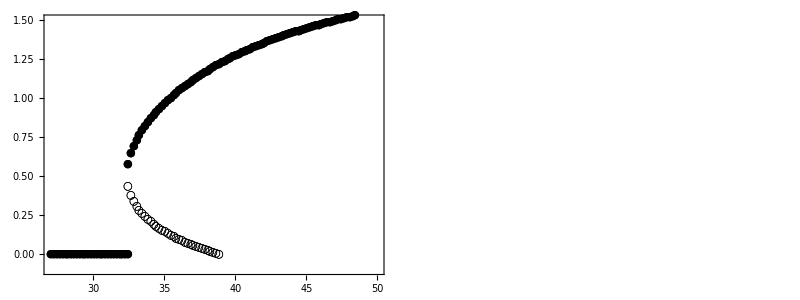

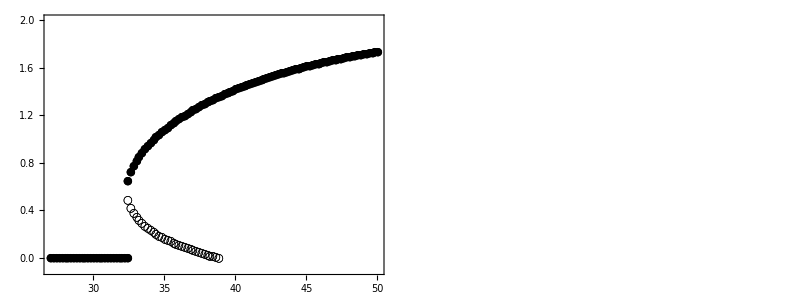

```mathematica
fwlist = fw/.Flatten[fwAllPositive, 1];
eqfwlist = eq/.Flatten[fwAllPositive, 1];

rangeIw = {{fwstart, fwend}, {-0.1, 1.5}};
rangeDw = {{fwstart, fwend}, {-0.001, 0.02}};

Iwfwlist = Iw/.eqfwlist;
MakeListPlotData[fwlist, Iwfwlist];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }], PlotStyle->Black,  PlotRange -> rangeIw, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{" ", "Density of singly infected intermediate host"},LabelStyle->labelStyle,FrameStyle->frameStyle];

Dwfwlist = Dw/.eqfwlist;
MakeListPlotData[fwlist, Dwfwlist];
p1 = ListPlot[%, PlotStyle->Black, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }], PlotRange->rangeDw, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{" ", "Density of singly infected definitive host"},LabelStyle->labelStyle,FrameStyle->frameStyle];


eqfwzero = ConstantArray[solsfwzero, Length[fwrange]];
MakeListPlotData[fwrange, Iw/.eqfwzero];
p2 = ListPlot[%, PlotStyle->Black, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, { "✶","○", "●" }], ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];

MakeListPlotData[fwrange, Dw/.eqfwzero];
p3 = ListPlot[%,PlotStyle ->Black, PlotMarkers-> ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, { "✶","○", "●" }], ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];

pp0 = Show[p0,  p2];
pp1 = Show[p1, p3];

rangeIww = {{fwstart, fwend}, {-0.1, 2}};
rangeDww = {{fwstart, fwend}, {-0.001, 0.05}};

Iwwfwlist = Iww/.eqfwlist;
MakeListPlotData[fwlist, Iwwfwlist + Iwfwlist];
p4 = ListPlot[%, PlotStyle->Black, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }], PlotRange->rangeIww, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Reproduction of sinly infected parasite", "Density of doubly infected definitive host"},LabelStyle->labelStyle,FrameStyle->frameStyle];
Dwwfwlist = Dww/.eqfwlist;
MakeListPlotData[fwlist, Dwwfwlist + Dwfwlist];
p5 = ListPlot[%, PlotStyle->Black, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }], PlotRange->rangeDww, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Reproduction of singly infected parasite", "Density of doubly infected definitive host"},LabelStyle->labelStyle,FrameStyle->frameStyle];

Grid[{{pp0, pp1}}]
Grid[{{Show[{p4, p2}], Show[{p5, p3}]}}]
```

## Parameter set 2

CALCULATION

```mathematica
parfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 1};
fwrangeFWrd = Range[40.5, 65, 0.2];
fwrangeBWrd = Range[40.5, 27, -0.2];
fwrange = Range[27, 50, 0.2];

(*Find all solutions of the system with the given parameter values*)
solsfwAll = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw/.fw-> 40.5) == 0], varRes, Reals];

(*Select disease circulation solutions*)
solsfw= Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)> 0 &&(Iww/.#)> 0 &&(W/.#)> 0 &][[1]];

(*Select disease free solutions*)
solsfwzero = Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];

eqfwFWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeFWrd, varRes, solsfw];
eqfwBWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeBWrd, varRes, solsfw];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

PLOTTING

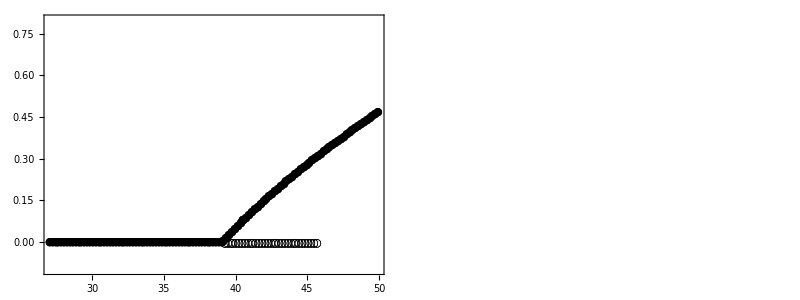

```mathematica
rangeIs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {-0.1, 0.8}};
rangeDs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {-0.002, 0.015}};

xaxis =fwrangeFWrd[[1;; Length[eqfwFWrd]]];
MakeListPlotData[xaxis, Iw/.eqfwFWrd];
p0 = ListPlot[%, PlotStyle->Black, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }], PlotRange->rangeIs, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Parasite reproduction in single infection", "Equilibrium of singly infected intermediate host"},LabelStyle->labelStyle,FrameStyle->frameStyle];

MakeListPlotData[xaxis, Dw/.eqfwFWrd];
p1 = ListPlot[%, PlotStyle->Black, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }], PlotRange->rangeDs, ImageSize->imageSize, Frame->includeFrame, FrameLabel->{"Parasite reproduction in single infection", "Equilibrium of singly infected definitive host"},LabelStyle->labelStyle,FrameStyle->frameStyle];

xaxis = fwrangeBWrd[[1;;Length[eqfwBWrd]]];
MakeListPlotData[xaxis, Iw/.eqfwBWrd];
p2 = ListPlot[%, PlotStyle->Black, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }], PlotRange->rangeIs, ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];

MakeListPlotData[xaxis, Dw/.eqfwBWrd];
p3 = ListPlot[%, PlotStyle->Black, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }], PlotRange->rangeDs, ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];


eqfwzero = ConstantArray[solsfwzero, Length[fwrange]];
MakeListPlotData[fwrange, Iw/.eqfwzero];
p4 = ListPlot[%, PlotStyle->Black, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, { "✶","○", "●" }], PlotRange->rangeIs, ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];

MakeListPlotData[fwrange, Dw/.eqfwzero];
p5 = ListPlot[%, PlotStyle->Black, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, { "✶","○", "●" }], PlotRange->rangeDs, ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];

ppp0 = Show[p0,  p2, p4];
ppp1 = Show[p1, p3, p5];

Grid[{{ppp0, ppp1}}]
(*Export["bifurcation_fw_NL.jpg", %]*)
```

## Combined plot parameter set 1 and parameter set 2

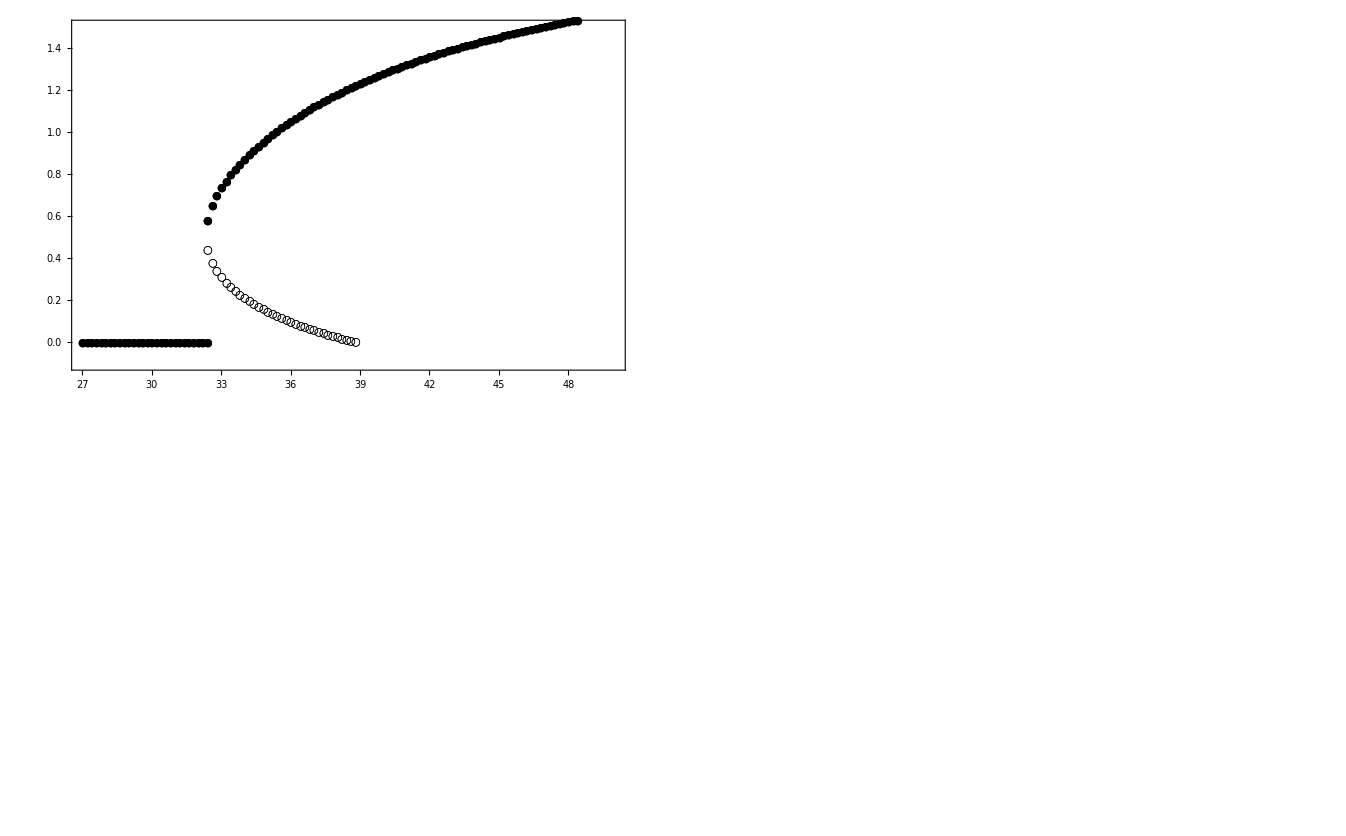

```mathematica
GraphicsGrid[{{pp0, pp1}, {ppp0, ppp1}}]
```

```mathematica
On[Assert];
rr= Range[36, 43, 0.02];
FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, rr, varRes, solsfwzero];
xx =ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, rr, %];
pos = Position[xx, "*", 1, 1][[1]][[1]];
xx[[pos]] == "*"//Assert
xx[[pos-1]] == "." //Assert
fwbifur = rr[[pos]]
```

38.96

## Bifurcation ϵ and f_w (f_ww = ϵ f_w)

CALCULATE

```mathematica
parϵfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26};

ϵstart = 0;
ϵend = 6;
ϵinterval = 0.5;
fwstart = 36;
fwend = 42;
fwinterval = 0.5;

ϵfwAllresults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parϵfw, {ϵ -> i}, {fw-> j}, ϵfw, eq,varRes,15],{i, ϵstart, ϵend, ϵinterval}, {j, fwstart, fwend, fwinterval}];
```

PLOT

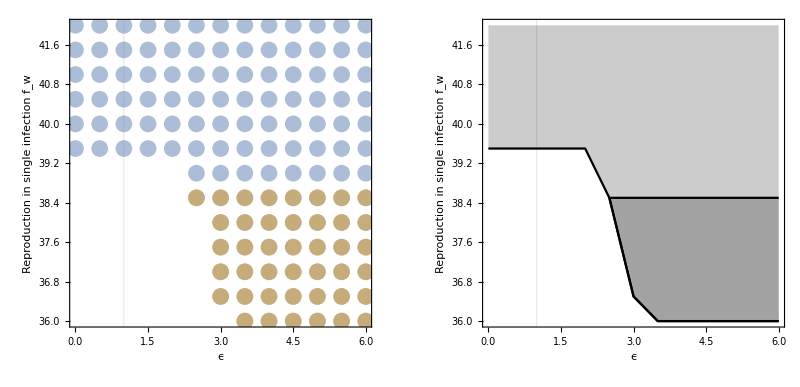

```mathematica
eqϵfw =eq/. Flatten[ϵfwAllresults, 2];
ϵfwlist = ϵfw/.Flatten[ϵfwAllresults, 2];
rangeϵfw= {{ϵstart , ϵend}, {fwstart , fwend}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parϵfw,{ϵ, fw}, ϵfwlist, eqϵfw, colorstable, True];
MakeListPlotData[ϵfwlist[[All, 1]], ϵfwlist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->rangeϵfw, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"ϵ", "Reproduction in single infection f_w"}, GridLines->{{1},{}}, GridLinesStyle-> {Thick,Black}, LabelStyle->labelStyle,FrameStyle->frameStyle,AspectRatio->1];
GetBoundaryLineBiStable[ϵfwlist];
p1 =ListLinePlot[%, AspectRatio->1, PlotRange->rangeϵfw, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"ϵ", "Reproduction in single infection f_w"}, LabelStyle->labelStyle,GridLines->{{1},{}}, GridLinesStyle-> {Thick,Black}, PlotStyle-> Black, Filling-> {1-> {2}}];
GetBoundaryLineSingle[ϵfwlist];
p2 = ListLinePlot[%, AspectRatio->1, PlotRange->rangeϵfw, Frame->includeFrame, FrameStyle->frameStyle, PlotStyle-> Black, Filling->Top];
GraphicsGrid[{{p0, Show[{p1, p2}]}}]
```

## Bifurcation of single and double infection (β_w and β_ww) setting f_ww=ϵ f_w

```mathematica
thick = 0.003;
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 17;
βwwstep = 0.3;
range= {{βwstart, βwend}, {βwwstart, βwwend}};
```

## Parameter set 1 (f_ww=f_w)

CALCULATE

```mathematica
parmanip1 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 1, fw -> 40};


manipAllResults1 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip1, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

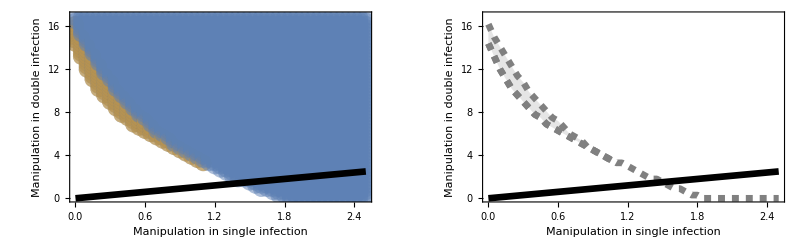

```mathematica
equilibrium =eq/. Flatten[manipAllResults1 , 2];
parslist = β/.Flatten[manipAllResults1, 2];
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip1,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle, ImageSize->imageSize];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle-> {Thickness[thick], Black}, ImageSize->imageSize];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle, PlotStyle->  {{Dashed, Thickness[thick], Gray},{Dashed,Thickness[thick], Gray}}, Filling-> {1-> {2}},(* PlotLegends->{"f_ww = f_w"}, *)ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Dashed, Thickness[thick], Gray}, ImageSize->imageSize];
l21 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, l21}}]
```

## Contour Plot for Reproduction ratio

### Reproduction ratio

```mathematica
R0func1 = R0/.func1/.Dw -> 0/.Dww-> 0/.Iw-> 0/.Iww-> 0//Simplify;
```

### Plot

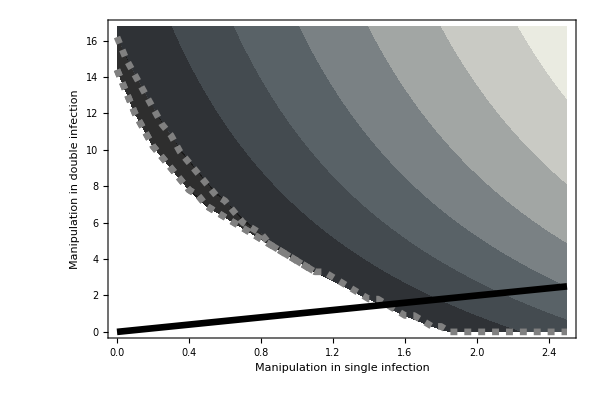

```mathematica
thick = 0.008;
Thread[sysfunc1==0]/.{Iw-> 0, Iww-> 0, Dw-> 0, Dww-> 0, W-> 0};
diseasefree = Solve[%, {Is, Ds}][[3]];
R0func1/.{Iw -> 0, Iww->0, Dw-> 0, Dww->0 , W-> 0}/.diseasefree/.fww-> ϵ fw/.parmanip1/. Thread[{Thread[βw->parslist[[All, 1]]],Thread[βww-> parslist[[All, 2]]]}];
Join[parslist, Partition[%, 1], 2];
R0g = ListContourPlot[%, PlotLegends->Automatic, Frame-> includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, ImageSize->imageSize, ColorFunction->"GrayTones", ContourStyle->None, AspectRatio->2/3, ContourStyle->None,PlotLegends->Placed[Automatic,Column]];

equilibrium =eq/. Flatten[manipAllResults1 , 2];
parslist = β/.Flatten[manipAllResults1, 2];
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip1,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
GetBoundaryLineBiStable[parslist];
p1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle, PlotStyle->  {{Dashed, Thickness[thick], Gray},{Dashed,Thickness[thick], Gray}}, Filling-> {1-> {2}},(* PlotLegends->{"f_ww = f_w"}, *)ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
p2= ListLinePlot[%, AspectRatio->1, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Dashed, Thickness[thick], Gray}];
p3 = Show[{p1,p2, p0}];

R0gfinal = Show[{ R0g, p3}]
```

## Combined R0 and manip bifurcation plot

1400

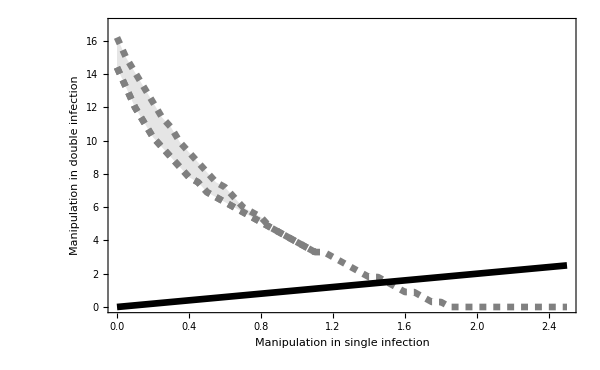

manip_bifur_R0.jpeg

```mathematica
imageSize = 1400
GraphicsRow[{l21, R0gfinal},Alignment->Top, ImageSize->imageSize]
(*Export[ "manip_bifur_R0.jpeg", %]*)
```

## Parameter set 2 (f_ww = 2 f_w)

CALCULATE

```mathematica
parmanip2 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 2, fw -> 38};

manipAllResults2 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip2, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

{{0,2.5},{0,17}}

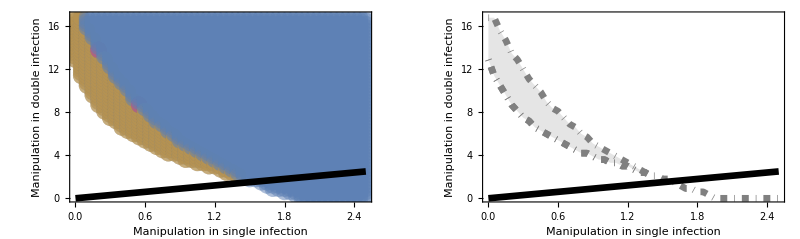

```mathematica
range
equilibrium =eq/. Flatten[manipAllResults2 , 2];
parslist = β/.Flatten[manipAllResults2, 2];
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip2,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"},  LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->{Thickness[thick], Black}];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle-> {{Thickness[thick], Gray, DotDashed}, {Thickness[thick], Gray, DotDashed}}, Filling-> {1-> {2}}(*, PlotLegends->{"f_ww = 2 f_w"}*), ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2 = ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {DotDashed,Thickness[thick], Gray}];
l22 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, l22}}]
```

## Parameter set 3 (f_ww = 0.5 f_w)

CALCULATE

```mathematica
parmanip3 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 0.5, fw -> 38};

manipAllResults3 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip3, {βw -> x}, {βww-> y}, β, eq,varRes, 14],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 6.740599975041793066. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -5.906851158804582385. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -2.737177720911923622. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

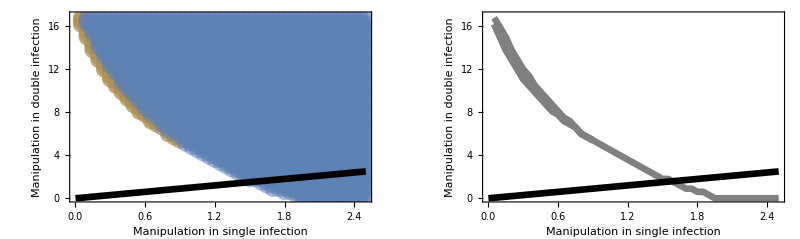

```mathematica
equilibrium =eq/. Flatten[manipAllResults3 , 2];
parslist = β/.Flatten[manipAllResults3, 2];
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip3,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"},  LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->{Thickness[thick], Black}];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle->{ {Thickness[thick], Gray}, {Thickness[thick], Gray}}, Filling-> {1-> {2}}(*, PlotLegends->{"f_ww = 0.5 f_w"}*), ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2 = ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], Gray}];
l23 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, l23}}]
```

## Combined plots

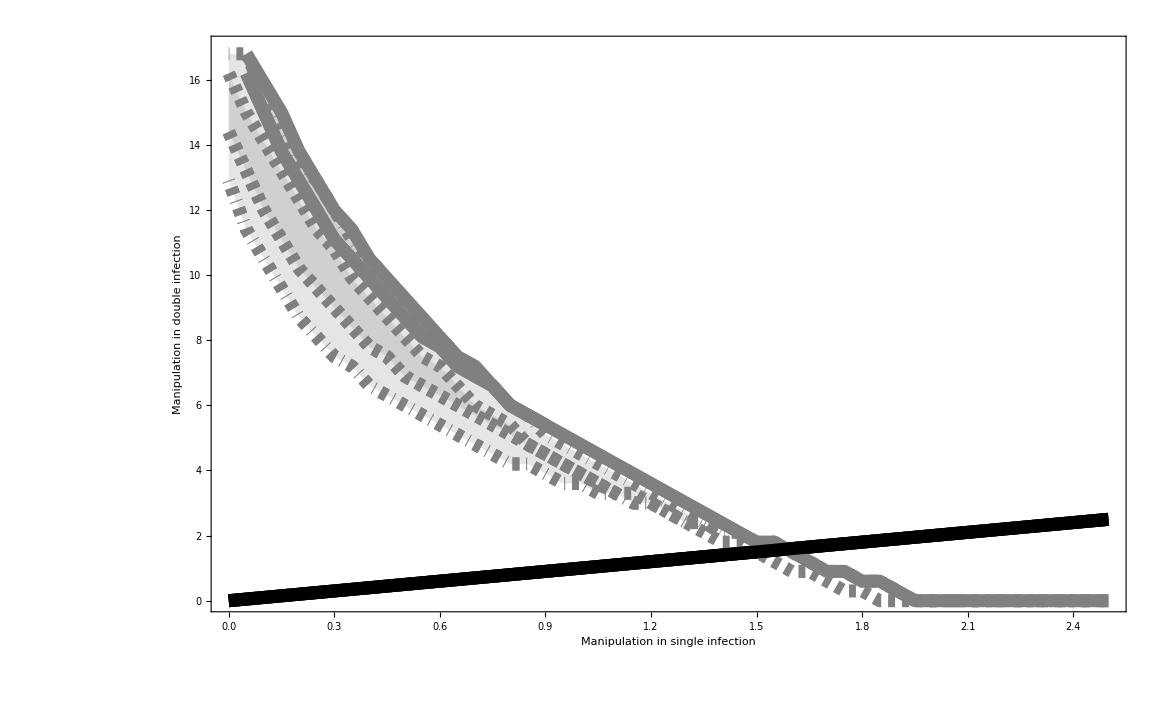

```mathematica
Show[{l22, l21,l23}]
Export["", ]
```

## Bifurcation of single and double infection (β_w and β_ww) with higher coinfection from parasite pool to intermediate host

```mathematica
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 2.5;
βwwstep = 0.05;
```

## Parameter set 1 (f_ww= f_w)

CALCULATION

```mathematica
parmanipHcoin1 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.5, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 1, fw -> 40};

manipHcoinAllResults1 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin1, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.85945431458445837. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

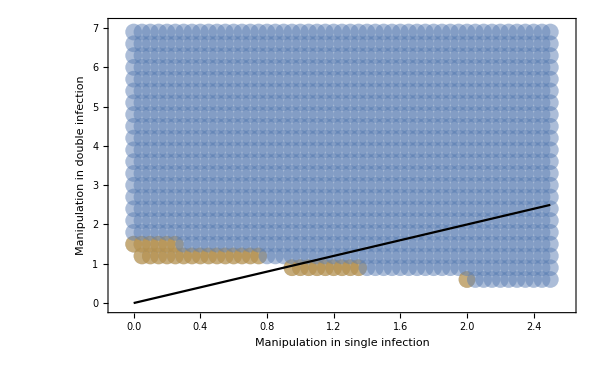

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults1 , 2];
parslist = β/.Flatten[manipHcoinAllResults1, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin1,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black, AspectRatio->1];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle->  {{Dashed, Thickness[thick], colorlist[[-1]]},{Dashed,Thickness[thick], colorlist[[-1]]}}, Filling-> {1-> {2}}, PlotLegends->{"f_ww = f_w"}, ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, AspectRatio->1, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle->  {{Dashed, Thickness[thick], colorlist[[-1]]},{Dashed,Thickness[thick], colorlist[[-1]]}}, Filling-> Top];
lHC21 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHC21}}]
```

## Parameter set 2 (f_ww = 2 f_w)

CALCULATION

```mathematica
parmanipHcoin2= {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.5, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 2, fw -> 40};

manipHcoinAllResults2 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin2, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

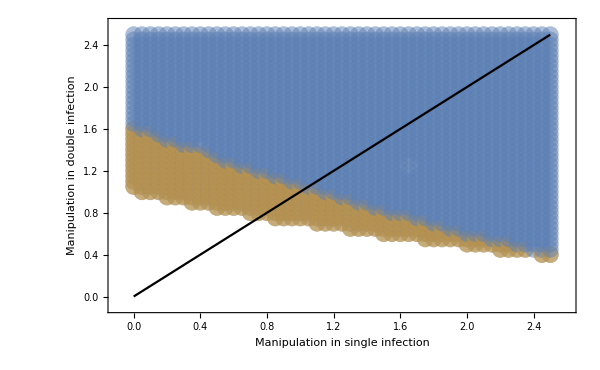

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults2 , 2];
parslist = β/.Flatten[manipHcoinAllResults2, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin2,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black, AspectRatio->1];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle-> {{DotDashed,Thickness[thick], colorlist[[1]]}, {DotDashed,Thickness[thick], colorlist[[1]]}}, Filling-> {1-> {2}}, PlotLegends->{"f_ww = 2 f_w"}, ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, AspectRatio->1, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {DotDashed,Thickness[thick], colorlist[[1]]}, Filling-> Top];
lHC22 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHC22}}]
```

## Parameter set 3 (f_ww = 0.5 f_w)

```mathematica
parmanipHcoin3= {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.5, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 0.5, fw -> 40};

manipHcoinAllResults3 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin3, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults3, 2];
parslist = β/.Flatten[manipHcoinAllResults3, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};


marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin3,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black, AspectRatio->1];
pp3 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle-> {{DotDashed,Thickness[thick], colorlist[[2]]}, {DotDashed,Thickness[thick], colorlist[[2]]}}, Filling-> {1-> {2}}, PlotLegends->{"f_ww = 0.5 f_w"}, ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, AspectRatio->1, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {DotDashed,Thickness[thick], colorlist[[2]]}, Filling-> Top];
lHC23 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp3, lHC23}}]
```

-Graphics-

## Combined plot

```mathematica
Show[{lHC21, lHC22, lHC23 }]
```

## Manipulation bifurcation graph when coinfection from intermediate to definitive host is high

```mathematica
thick = 0.003;
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 17;
βwwstep = 0.4;
```

## Parameter set 1 (f_ww= f_w)

CALCULATE

```mathematica
parmanipHcoin4 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.3, δ-> 0.9, k -> 0.26, ϵ-> 1, fw -> 40};

manipHcoinAllResults4 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin4, {βw -> x}, {βww-> y}, β, eq,varRes, 12],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

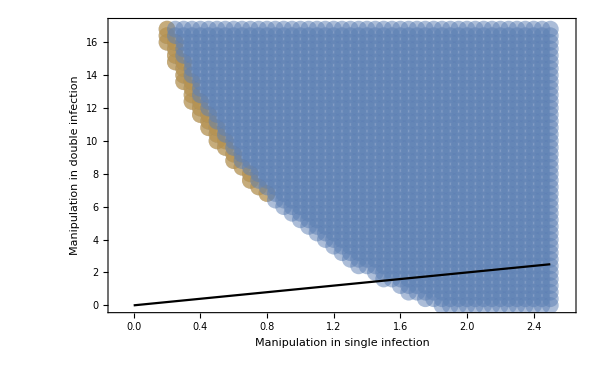

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults4 , 2];
parslist = β/.Flatten[manipHcoinAllResults4, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin4,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black, AspectRatio->1];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle->  {{Dashed, Thickness[thick], colorlist[[-1]]},{Dashed,Thickness[thick], colorlist[[-1]]}}, Filling-> {1-> {2}}, PlotLegends->{"f_ww = f_w"}, ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, AspectRatio->1, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle->  {{Dashed, Thickness[thick], colorlist[[-1]]},{Dashed,Thickness[thick], colorlist[[-1]]}}, Filling-> Top];
lHC21 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHC21}}]
```

## Parameter set 2 (fww = 2 fw)

CALCULATE

```mathematica
parmanipHcoin5 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.3, δ-> 0.9, k -> 0.26, ϵ-> 2, fw -> 40};

manipHcoinAllResults5 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin5, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.114331652260201863. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.11394057232571976. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -12.32632248972310585. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.8985222312110403739. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.682243789376203276. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.85942002496627856. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -2.4327313419704206237. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -31.206010779026839167+0. ⅈ. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

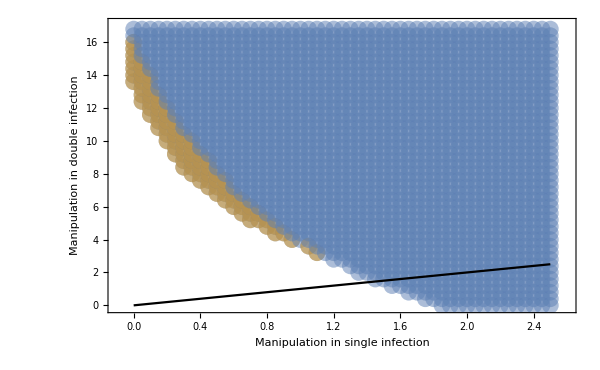

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults5 , 2];
parslist = β/.Flatten[manipHcoinAllResults5, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin5,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black, AspectRatio->1];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle-> {{DotDashed,Thickness[thick], colorlist[[1]]}, {DotDashed,Thickness[thick], colorlist[[1]]}}, Filling-> {1-> {2}}, PlotLegends->{"f_ww = 2 f_w"}, ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, AspectRatio->1, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {DotDashed,Thickness[thick], colorlist[[1]]}, Filling-> Top];
lHC22 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHC22}}]
```

## Parameter set 3 (fww = 0.5 fw)

CALCULATE

```mathematica
parmanipHcoin6 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.3, δ-> 0.9, k -> 0.26, ϵ-> 0.5, fw -> 40};

manipHcoinAllResults6 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin6, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -5.546123675032574843. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.11440046554870628. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859432446590739176. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.113936175810711. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.310056072006026. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.85941734279573629. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

General::stop: Further output of NSolve::sfail will be suppressed during this calculation.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -371.96504843181118+0. ⅈ. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

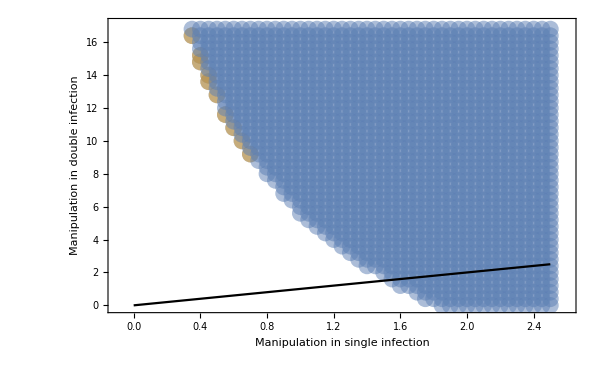

```mathematica
equilibrium =eq/. Flatten[manipHcoinAllResults6, 2];
parslist = β/.Flatten[manipHcoinAllResults6, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};


marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin6,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black, AspectRatio->1];
pp3 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle-> {{DotDashed,Thickness[thick], colorlist[[2]]}, {DotDashed,Thickness[thick], colorlist[[2]]}}, Filling-> {1-> {2}}, PlotLegends->{"f_ww = 0.5 f_w"}, ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, AspectRatio->1, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {DotDashed,Thickness[thick], colorlist[[2]]}, Filling-> Top];
lHC23 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp3, lHC23}}]
```

## Combined plot

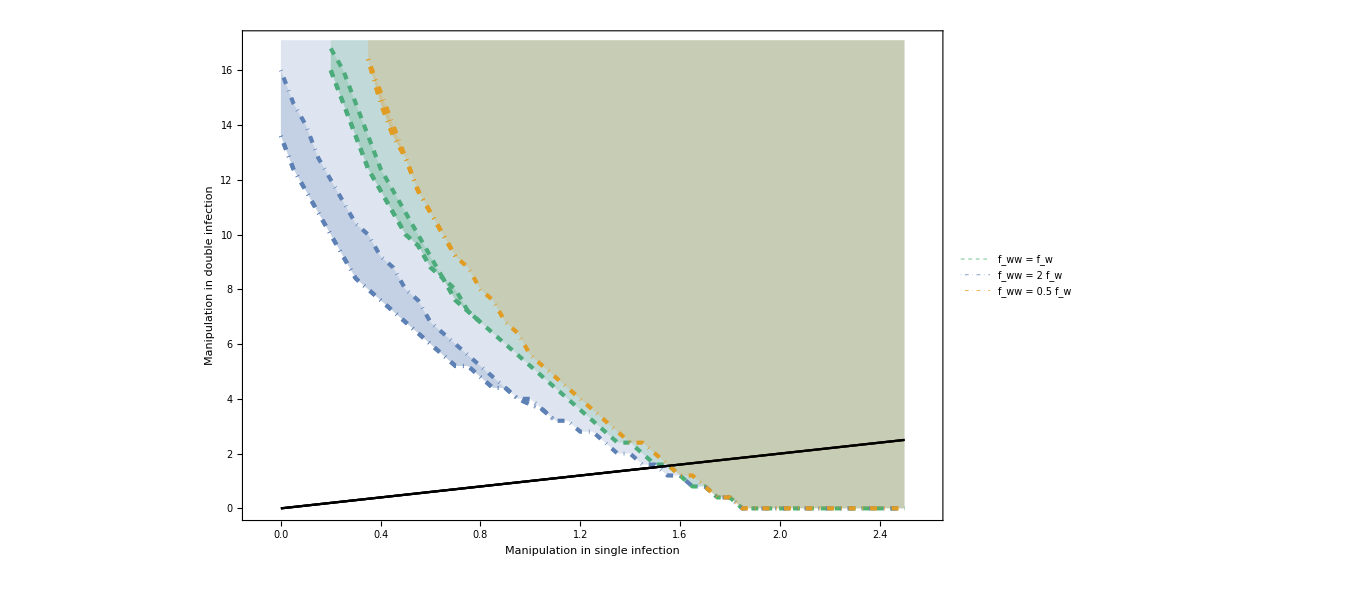

manip_bifur_q.jpeg

```mathematica
Show[{lHC21, lHC22, lHC23 }]
```